```mathematica
omega=1;
rad=0.1;
len=100;
x0=0; xf=8; y0=0; yf=4;
y1=5; y1f=9;

Show[
DensityPlot[ Pi x,{x,x0,xf},{y,y0,yf},{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase]/2,0.5+Sin[phase]/2,0]]},ColorFunctionScaling->False, AspectRatio->1/4,Frame->True,FrameTicks->{True,False}, ImageSize->Large,PlotPoints->400],
DensityPlot[ Pi x,{x,x0,xf},{y,y1,y1f},{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase]/2,0.5+Sin[phase]/2,0]]},ColorFunctionScaling->False, AspectRatio->1/4,Frame->True,FrameTicks->{True,False}, ImageSize->Large,PlotPoints->400]
]
```

-Graphics-

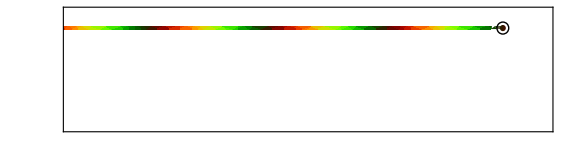

```mathematica
x0=7.3; y0=1.7; 
Show[
DensityPlot[ Pi x,{x,y}∈Disk[{x0,y0},rad+.05],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase]/2,0.5+Sin[phase]/2,0]]},ColorFunctionScaling->False, AspectRatio->1/4,Frame->True,FrameTicks->False, ImageSize->Large,PlotRange->{{0,8},{0,2}}],
Graphics[{Thickness[0.01],White,Circle[{x0,y0},rad+.02]}],
DensityPlot[ Pi x,{x,y}∈Rectangle[{x0-len,y0-rad/4},{x0,y0+rad/4}],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase]/2,0.5+Sin[phase]/2,0]]},ColorFunctionScaling->False],Graphics[{Thick,Black,Circle[{x0,y0},rad]}]
]
```

```mathematica
omega=1;
rad=0.2;
len=100;
x0=5; xf=8; y0=1; yf=2;
thetarange=Range[0,omega* 20,1/10];

movievector =ConstantArray[0,Length[thetarange]];
For[t=1,t<Length[thetarange],t++,

x1=-17.3+2*thetarange[[t]]; y1=0.05; 
x2=-5.6+2*thetarange[[t]]; y2=0.15;
x3=-10.8+2*thetarange[[t]]; y3=0.25;
x4=-3+2*thetarange[[t]]; y4=0.35;
x5=-16.4+2*thetarange[[t]]; y5=0.45;
x6=-22+2*thetarange[[t]]; y6=0.55;
x7=-13.1+2*thetarange[[t]]; y7=0.65; 
x8=-17.9+2*thetarange[[t]]; y8=0.75;
x9=-12.3+2*thetarange[[t]]; y9=0.85;
x10=-19.6+2*thetarange[[t]]; y10=0.95;
x11=-10+2*thetarange[[t]]; y11=1.05;
x12=3.3+2*thetarange[[t]]; y12=1.15;
x13=-13.4+2*thetarange[[t]]; y13=1.25;
x14=-7.7+2*thetarange[[t]]; y14=1.35;
x15=-5.3+2*thetarange[[t]]; y15=1.45; 
x16=-18.4+2*thetarange[[t]]; y16=1.55;
x17=4.7+2*thetarange[[t]]; y17=1.65;
x18=-11.7+2*thetarange[[t]]; y18=1.75;
x19=-6.5+2*thetarange[[t]]; y19=1.85;
x20=-14.9+2*thetarange[[t]]; y20=1.95;

movievector[[t]]=Show[

DensityPlot[ Pi x,{x,y}∈Disk[{x1,y1},rad/2],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase-thetarange[[t]]]/2,0]]},ColorFunctionScaling->False, AspectRatio->1/4,Frame->True,FrameTicks->False, ImageSize->Large,PlotPoints->400,PlotRange->{{0,8},{0,2}}],

DensityPlot[ Pi x,{x,y}∈Rectangle[{x1-len,y1-rad/4},{x1,y1+rad/4}],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase -thetarange[[t]] ]/2,0]]},ColorFunctionScaling->False],Graphics[{Thick,Black,Circle[{x1,y1},rad/2]}],

DensityPlot[ Pi x,{x,y}∈Disk[{x2,y2},rad/2],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase-thetarange[[t]]]/2,0]]},ColorFunctionScaling->False, AspectRatio->1/4,Frame->True,FrameTicks->False, ImageSize->Large,PlotPoints->400,PlotRange->{{0,8},{0,2}}],

DensityPlot[ Pi x,{x,y}∈Rectangle[{x2-len,y2-rad/4},{x2,y2+rad/4}],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase -thetarange[[t]] ]/2,0]]},ColorFunctionScaling->False],Graphics[{Thick,Black,Circle[{x2,y2},rad/2]}],

DensityPlot[ Pi x,{x,y}∈Disk[{x3,y3},rad/2],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase-thetarange[[t]]]/2,0]]},ColorFunctionScaling->False, AspectRatio->1/4,Frame->True,FrameTicks->False, ImageSize->Large,PlotPoints->400,PlotRange->{{0,8},{0,2}}],

DensityPlot[ Pi x,{x,y}∈Rectangle[{x3-len,y3-rad/4},{x3,y3+rad/4}],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase -thetarange[[t]] ]/2,0]]},ColorFunctionScaling->False],Graphics[{Thick,Black,Circle[{x3,y3},rad/2]}],

DensityPlot[ Pi x,{x,y}∈Disk[{x4,y4},rad/2],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase-thetarange[[t]]]/2,0]]},ColorFunctionScaling->False, AspectRatio->1/4,Frame->True,FrameTicks->False, ImageSize->Large,PlotPoints->400,PlotRange->{{0,8},{0,2}}],

DensityPlot[ Pi x,{x,y}∈Rectangle[{x4-len,y4-rad/4},{x4,y4+rad/4}],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase -thetarange[[t]] ]/2,0]]},ColorFunctionScaling->False],Graphics[{Thick,Black,Circle[{x4,y4},rad/2]}],

DensityPlot[ Pi x,{x,y}∈Disk[{x5,y5},rad/2],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase-thetarange[[t]]]/2,0]]},ColorFunctionScaling->False, AspectRatio->1/4,Frame->True,FrameTicks->False, ImageSize->Large,PlotPoints->400,PlotRange->{{0,8},{0,2}}],

DensityPlot[ Pi x,{x,y}∈Rectangle[{x5-len,y5-rad/4},{x5,y5+rad/4}],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase -thetarange[[t]] ]/2,0]]},ColorFunctionScaling->False],Graphics[{Thick,Black,Circle[{x5,y5},rad/2]}],

DensityPlot[ Pi x,{x,y}∈Disk[{x6,y6},rad/2],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase-thetarange[[t]]]/2,0]]},ColorFunctionScaling->False, AspectRatio->1/4,Frame->True,FrameTicks->False, ImageSize->Large,PlotPoints->400,PlotRange->{{0,8},{0,2}}],

DensityPlot[ Pi x,{x,y}∈Rectangle[{x6-len,y6-rad/4},{x6,y6+rad/4}],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase -thetarange[[t]] ]/2,0]]},ColorFunctionScaling->False],Graphics[{Thick,Black,Circle[{x6,y6},rad/2]}],

DensityPlot[ Pi x,{x,y}∈Disk[{x7,y7},rad/2],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase-thetarange[[t]]]/2,0]]},ColorFunctionScaling->False, AspectRatio->1/4,Frame->True,FrameTicks->False, ImageSize->Large,PlotPoints->400,PlotRange->{{0,8},{0,2}}],

DensityPlot[ Pi x,{x,y}∈Rectangle[{x7-len,y7-rad/4},{x7,y7+rad/4}],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase -thetarange[[t]] ]/2,0]]},ColorFunctionScaling->False],Graphics[{Thick,Black,Circle[{x7,y7},rad/2]}],

DensityPlot[ Pi x,{x,y}∈Disk[{x8,y8},rad/2],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase-thetarange[[t]]]/2,0]]},ColorFunctionScaling->False, AspectRatio->1/4,Frame->True,FrameTicks->False, ImageSize->Large,PlotPoints->400,PlotRange->{{0,8},{0,2}}],

DensityPlot[ Pi x,{x,y}∈Rectangle[{x8-len,y8-rad/4},{x8,y8+rad/4}],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase -thetarange[[t]] ]/2,0]]},ColorFunctionScaling->False],Graphics[{Thick,Black,Circle[{x8,y8},rad/2]}],

DensityPlot[ Pi x,{x,y}∈Disk[{x9,y9},rad/2],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase-thetarange[[t]]]/2,0]]},ColorFunctionScaling->False, AspectRatio->1/4,Frame->True,FrameTicks->False, ImageSize->Large,PlotPoints->400,PlotRange->{{0,8},{0,2}}],

DensityPlot[ Pi x,{x,y}∈Rectangle[{x9-len,y9-rad/4},{x9,y9+rad/4}],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase -thetarange[[t]] ]/2,0]]},ColorFunctionScaling->False],Graphics[{Thick,Black,Circle[{x9,y9},rad/2]}],

DensityPlot[ Pi x,{x,y}∈Disk[{x10,y10},rad/2],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase-thetarange[[t]]]/2,0]]},ColorFunctionScaling->False, AspectRatio->1/4,Frame->True,FrameTicks->False, ImageSize->Large,PlotPoints->400,PlotRange->{{0,8},{0,2}}],

DensityPlot[ Pi x,{x,y}∈Rectangle[{x10-len,y10-rad/4},{x10,y10+rad/4}],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase -thetarange[[t]] ]/2,0]]},ColorFunctionScaling->False],Graphics[{Thick,Black,Circle[{x10,y10},rad/2]}],

DensityPlot[ Pi x,{x,y}∈Disk[{x11,y11},rad/2],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase-thetarange[[t]]]/2,0]]},ColorFunctionScaling->False, AspectRatio->1/4,Frame->True,FrameTicks->False, ImageSize->Large,PlotPoints->400,PlotRange->{{0,8},{0,2}}],

DensityPlot[ Pi x,{x,y}∈Rectangle[{x11-len,y11-rad/4},{x11,y11+rad/4}],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase -thetarange[[t]] ]/2,0]]},ColorFunctionScaling->False],Graphics[{Thick,Black,Circle[{x11,y11},rad/2]}],

DensityPlot[ Pi x,{x,y}∈Disk[{x12,y12},rad/2],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase-thetarange[[t]]]/2,0]]},ColorFunctionScaling->False, AspectRatio->1/4,Frame->True,FrameTicks->False, ImageSize->Large,PlotPoints->400,PlotRange->{{0,8},{0,2}}],

DensityPlot[ Pi x,{x,y}∈Rectangle[{x12-len,y12-rad/4},{x12,y12+rad/4}],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase -thetarange[[t]] ]/2,0]]},ColorFunctionScaling->False],Graphics[{Thick,Black,Circle[{x12,y12},rad/2]}],

DensityPlot[ Pi x,{x,y}∈Disk[{x13,y13},rad/2],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase-thetarange[[t]]]/2,0]]},ColorFunctionScaling->False, AspectRatio->1/4,Frame->True,FrameTicks->False, ImageSize->Large,PlotPoints->400,PlotRange->{{0,8},{0,2}}],

DensityPlot[ Pi x,{x,y}∈Rectangle[{x13-len,y13-rad/4},{x13,y13+rad/4}],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase -thetarange[[t]] ]/2,0]]},ColorFunctionScaling->False],Graphics[{Thick,Black,Circle[{x13,y13},rad/2]}],

DensityPlot[ Pi x,{x,y}∈Disk[{x14,y14},rad/2],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase-thetarange[[t]]]/2,0]]},ColorFunctionScaling->False, AspectRatio->1/4,Frame->True,FrameTicks->False, ImageSize->Large,PlotPoints->400,PlotRange->{{0,8},{0,2}}],

DensityPlot[ Pi x,{x,y}∈Rectangle[{x14-len,y14-rad/4},{x14,y14+rad/4}],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase -thetarange[[t]] ]/2,0]]},ColorFunctionScaling->False],Graphics[{Thick,Black,Circle[{x14,y14},rad/2]}],

DensityPlot[ Pi x,{x,y}∈Disk[{x15,y15},rad/2],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase-thetarange[[t]]]/2,0]]},ColorFunctionScaling->False, AspectRatio->1/4,Frame->True,FrameTicks->False, ImageSize->Large,PlotPoints->400,PlotRange->{{0,8},{0,2}}],

DensityPlot[ Pi x,{x,y}∈Rectangle[{x15-len,y15-rad/4},{x15,y15+rad/4}],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase -thetarange[[t]] ]/2,0]]},ColorFunctionScaling->False],Graphics[{Thick,Black,Circle[{x15,y15},rad/2]}],

DensityPlot[ Pi x,{x,y}∈Disk[{x16,y16},rad/2],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase-thetarange[[t]]]/2,0]]},ColorFunctionScaling->False, AspectRatio->1/4,Frame->True,FrameTicks->False, ImageSize->Large,PlotPoints->400,PlotRange->{{0,8},{0,2}}],

DensityPlot[ Pi x,{x,y}∈Rectangle[{x16-len,y16-rad/4},{x16,y16+rad/4}],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase -thetarange[[t]] ]/2,0]]},ColorFunctionScaling->False],Graphics[{Thick,Black,Circle[{x16,y16},rad/2]}],

DensityPlot[ Pi x,{x,y}∈Disk[{x17,y17},rad/2],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase-thetarange[[t]]]/2,0]]},ColorFunctionScaling->False, AspectRatio->1/4,Frame->True,FrameTicks->False, ImageSize->Large,PlotPoints->400,PlotRange->{{0,8},{0,2}}],

DensityPlot[ Pi x,{x,y}∈Rectangle[{x17-len,y17-rad/4},{x17,y17+rad/4}],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase -thetarange[[t]] ]/2,0]]},ColorFunctionScaling->False],Graphics[{Thick,Black,Circle[{x17,y17},rad/2]}],

DensityPlot[ Pi x,{x,y}∈Disk[{x18,y18},rad/2],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase-thetarange[[t]]]/2,0]]},ColorFunctionScaling->False, AspectRatio->1/4,Frame->True,FrameTicks->False, ImageSize->Large,PlotPoints->400,PlotRange->{{0,8},{0,2}}],

DensityPlot[ Pi x,{x,y}∈Rectangle[{x18-len,y18-rad/4},{x18,y18+rad/4}],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase -thetarange[[t]] ]/2,0]]},ColorFunctionScaling->False],Graphics[{Thick,Black,Circle[{x18,y18},rad/2]}],

DensityPlot[ Pi x,{x,y}∈Disk[{x19,y19},rad/2],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase-thetarange[[t]]]/2,0]]},ColorFunctionScaling->False, AspectRatio->1/4,Frame->True,FrameTicks->False, ImageSize->Large,PlotPoints->400,PlotRange->{{0,8},{0,2}}],

DensityPlot[ Pi x,{x,y}∈Rectangle[{x19-len,y19-rad/4},{x19,y19+rad/4}],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase -thetarange[[t]] ]/2,0]]},ColorFunctionScaling->False],Graphics[{Thick,Black,Circle[{x19,y19},rad/2]}],

DensityPlot[ Pi x,{x,y}∈Disk[{x20,y20},rad/2],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase-thetarange[[t]]]/2,0]]},ColorFunctionScaling->False, AspectRatio->1/4,Frame->True,FrameTicks->False, ImageSize->Large,PlotPoints->400,PlotRange->{{0,8},{0,2}}],

DensityPlot[ Pi x,{x,y}∈Rectangle[{x20-len,y20-rad/4},{x20,y20+rad/4}],{ColorFunction->Function[{phase},RGBColor[0.5+Cos[phase-thetarange[[t]]]/2,0.5+Sin[phase -thetarange[[t]] ]/2,0]]},ColorFunctionScaling->False],Graphics[{Thick,Black,Circle[{x20,y20},rad/2]}]

]
]
fileName="1D_animation_2panel.avi";
Export[fileName,movievector];
Directory[];
```

$Aborted